# Practica numero 2

## Ejercicio numero 1

```mathematica
Expand[(a+b)^5]
```

a^5+5 a^4 b+10 a^3 b^2+10 a^2 b^3+5 a b^4+b^5

## Ejercicio numero 2

```mathematica
f1[x_]=-x^3;
f2[x_]=2 x-12;
interseccionn=x/. Solve[f1[x_]==f2[x_],x_]

Plot[{f1[x],f2[x]},{x,-5,5},Epilog->{Red,PointSize[0.02],Point[{interseccionn,f1[interseccionn]}]},PlotLegends->{"f1(x)","f2(x)","Intersección"}]
```

{2,-1-ⅈ √5,-1+ⅈ √5}

-Graphics-

## Ejercicio 3

La ecuación de la asíntota horizontal es: y = 5

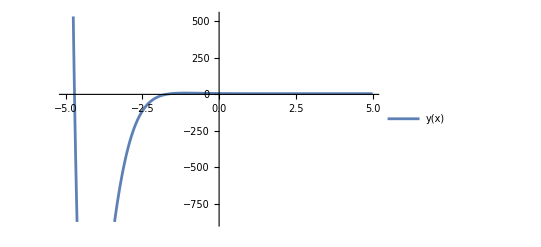

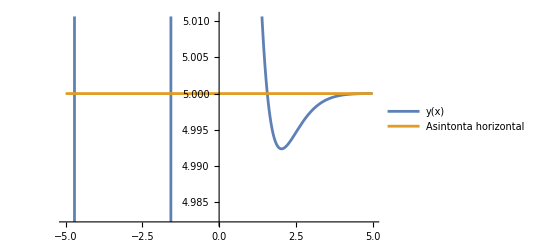

```mathematica
y[x_]=5+Exp[-2x]Cos[x];
limite=Limit[y[x],x->Infinity];
Print["La ecuación de la asíntota horizontal es: y = ",limite]


Plot[{y[x]},{x,- 5,5},PlotLegends->{"y(x)"}]
Plot[{y[x],limite},{x,- 5,5},PlotLegends->{"y(x)","Asintonta horizontal"}]
```

## Ejercicio 4

```mathematica
g[t_]=t^3;
t[x_]=Sqrt[x-5];
h[x]=g[t[x]]
f[x]=g[x] t[x]
```

(-5+x)^(3/2)

√(-5+x) x^3

## Ejercicio 5

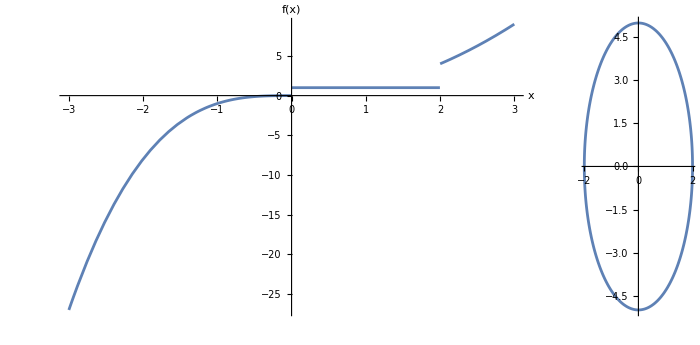

-Graphics3D-

```mathematica
f[x_]=Piecewise[{{x^3,x<=0},{1,0<x<2},{x^2,x>=2}}];
grafica1=Plot[f[x],{x,-3,3},PlotRange->All,AxesLabel->{"x","f(x)"}];

x[t_]=2Cos[t];
y[t_]=5Sin[t];
grafica2=ParametricPlot[{x[t],y[t]},{t,0,2 Pi}];
GraphicsRow[{grafica1,grafica2},ImageSize->700]

ParametricPlot3D[{5*Sin[theta]*Cos[phi],5*Sin[theta]*Sin[phi],5*Cos[theta]},{theta,0,Pi},{phi,0,2 Pi},PlotStyle->Thick,PlotTheme->"Classic"]
```

## Ejercicio 6

```mathematica
raices=NSolve[x==x^2 Sin[x]&&0<=x<=10,x];
```

NSolve::ivar: Sin[TerminatedEvaluation[RecursionLimit]]^2 Sin[Sin[TerminatedEvaluation[RecursionLimit]] TerminatedEvaluation[RecursionLimit]^2] TerminatedEvaluation[RecursionLimit]^4 is not a valid variable.

## Ejercicio 7

```mathematica
f[x_]:=Cos[3 x]-Cos[7 x]
sol=x/. FindRoot[f[x]==0,{x,1,1.5},WorkingPrecision->6]
Print["La solución positiva más pequeña de la ecuación cos(3x) = cos(7x) en el intervalo [0.5, 1.5] con una precisión de 6 cifras es: ",sol]
```

1.25664

La solución positiva más pequeña de la ecuación cos(3x) = cos(7x) en el intervalo [0.5, 1.5] con una precisión de 6 cifras es: 1.25664